Задача 7
Определить круг сходимости заданного степенного ряда. Сходится ли ряд в точке z1,z2,z3? Если сходится, то как - абсолютно или условно? Сделать рисунок.
Дан ряд:

```mathematica
∑_(n=1)^∞ (z-2 ⅈ)^(2 n-1)/((n+1)^2 log(n+1)) , z1=0, z2=3i, z3=1+2i
```

Для того чтобы найти область сходимости воспользуемся критерием Коши:

```mathematica
lim_(n->∞) Abs[z-2 ⅈ]^((2 n-1)/n)/(((n+1)^2 log(n+1))^(1/n))
```

Abs[-2 ⅈ+z]^2

Отсюда область сходимости:

```mathematica
|z-2i|^2<1    =>   |z-2i|<1
```

Изобразим полученный ответ:

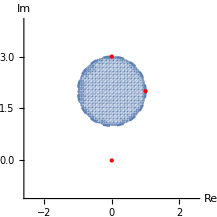

```mathematica
Show[RegionPlot[x^2+(y-2)^2<1,{x,-1,1},{y,1,3},AxesLabel->{Re,Im},PlotRange->{{-2.5,2.5},{-1,4}} ,Frame->False,
Axes->True,BoundaryStyle->Dashed],Graphics[{PointSize[Large],Red,Point[{{0,0},{0,3},{1,2}}]}]]
```

Теперь исследуем сходимость ряда в точках z1,z2,z3.
Точку z1=0 можно сразу исключить, так как она не попадает в область сходимости.
Рассмотрим точку z1=3i

```mathematica
∑_(n=1)^∞ (z-2 ⅈ)^(2 n-1)/((n+1)^2 log(n+1))/.z->3I
```

∑_(n=1)^∞ ⅈ^(-1+2 n)/((1+n)^2 Log[1+n])

Исследуем на абсолютную сходимость сходимость при помощи интегрального признака Коши:

```mathematica
∫_1^∞ 1/((n+1)^2 log(n+1))ⅆn //N
```

0.378671

Интеграл является сходящимся, следовательно в точке z=3I ряд сходится абсолютно.
Исследуем ряд в точке z=1+2I

```mathematica
∑_(n=1)^∞ (z-2 ⅈ)^(2 n-1)/((n+1)^2 log(n+1))/.z->1+2I
```

∑_(n=1)^∞ 1/((1+n)^2 Log[1+n])

Уже было получено что данный ряд сходится абсолютно, следовательно в точке z=1+2I ряд также сходится абсолютно.